## Basic Syntax and Operation

```mathematica
{1, 2, 3}
```

{1,2,3}

```mathematica
MyList = {a, 1, 2, "Cat", {1, 2,3}}
```

{a,1,2,Cat,{1,2,3}}

```mathematica
?Range
```

Range[i_max] generates the list {1,2,…,i_max}. 
Range[i_min,i_max] generates the list {i_min,…,i_max}. 
Range[i_min,i_max,di] uses step di.

```mathematica
?Length
```

Length[expr] gives the number of elements in expr.

```mathematica
u = Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
u
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
v = Range[11, 20]
```

{11,12,13,14,15,16,17,18,19,20}

```mathematica
u - v
```

{-10,-10,-10,-10,-10,-10,-10,-10,-10,-10}

```mathematica
u + v
```

{12,14,16,18,20,22,24,26,28,30}

```mathematica
Sqrt[u]
```

{1,√2,√3,2,√5,√6,√7,2 √2,3,√10}

```mathematica
N[Sqrt[u]]
```

{1.,1.41421,1.73205,2.,2.23607,2.44949,2.64575,2.82843,3.,3.16228}

### Generating List

```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

```mathematica
Table[{i, Sin[i]}, {i, 1, 10, 0.001}]
```

{{1.,0.841471},{1.001,0.842011},{1.002,0.84255},{1.003,0.843088},{1.004,0.843625},8991,{9.996,-0.54066},{9.997,-0.541501},{9.998,-0.542342},{9.999,-0.543182},{10.,-0.544021}}
 |  |  |  |

```mathematica
?Depth
```

Depth[expr] gives the maximum number of indices needed to specify any part of expr, plus 1.

```mathematica
?Flatten
```

Flatten[list] flattens out nested lists. 
Flatten[list,n] flattens to level n. 
Flatten[list,n,h] flattens subexpressions with head h. 
Flatten[list,{{s_11,s_12,…},{s_21,s_22,…},…}] flattens list by combining all levels s_ij to make each level i in the result.

```mathematica
?Partition
```

Partition[list,n] partitions list into nonoverlapping sublists of length n. 
Partition[list,n,d] generates sublists with offset d. 
Partition[list,{n_1,n_2,…}] partitions a nested list into blocks of size n_1×n_2×….
Partition[list,{n_1,n_2,…},{d_1,d_2,…}] uses offset d_i at level i in list. 
Partition[list,n,d,{k_L,k_R}] specifies that the first element of list should appear at position k_L in the first sublist, and the last element of list should appear at or after position k_R in the last sublist. If additional elements are needed, Partition fills them in by treating list as cyclic. 
Partition[list,n,d,{k_L,k_R},x] pads if necessary by repeating the element x. 
Partition[list,n,d,{k_L,k_R},{x_1,x_2,…}] pads if necessary by cyclically repeating the elements x_i. 
Partition[list,n,d,{k_L,k_R},{}] uses no padding, and so can yield sublists of different lengths. 
Partition[list,nlist,dlist,{klist_L,klist_R},padlist] specifies alignments and padding in a nested list.

```mathematica
?Part
```

expr[[i]] or Part[expr,i] gives the i^th part of expr. 
expr[[-i]] counts from the end. 
expr[[i,j,…]] or Part[expr,i,j,…] is equivalent to expr[[i]][[j]]…. 
expr[[{i_1,i_2,…}]] gives a list of the parts i_1, i_2, … of expr. 
expr[[m;;n]] gives parts m through n.
expr[[m;;n;;s]] gives parts m through n in steps of s.
expr[[key]] gives the value associated with the key "key" in an association expr.
expr[[Key[k]]] gives the value associated with an arbitrary key k in the association expr.

```mathematica
alpha = Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
alpha
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
alpha = Append[alpha, "Last Element"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Last Element}

```mathematica
alpha = Prepend[alpha, "First Element"]
```

{First Element,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Last Element}

```mathematica
alpha = Insert[alpha, "4th Element", 4]
```

{First Element,a,b,4th Element,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Last Element}

```mathematica
alpha
```

{First Element,a,b,4th Element,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Last Element}

```mathematica
?Delete
```

Delete[expr,n] deletes the element at position n in expr. If n is negative, the position is counted from the end. 
Delete[expr,{i,j,…}] deletes the part at position {i,j,…}. 
Delete[expr,{{i_1,j_1,…},{i_2,j_2,…},…}] deletes parts at several positions. 
Delete[pos] represents an operator form of Delete that can be applied to an expression.

```mathematica
Delete[alpha, 1]
```

{a,b,4th Element,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Last Element}

```mathematica
range1 = Range[1, 10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
range2 = Range[15, 7, -1]
```

{15,14,13,12,11,10,9,8,7}

```mathematica
joined = Join[range1, range2]
```

{1,2,3,4,5,6,7,8,9,10,15,14,13,12,11,10,9,8,7}

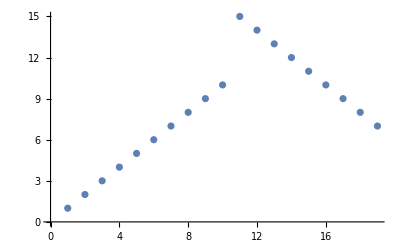

```mathematica
ListPlot[joined]
```

```mathematica
?DeleteDuplicates
```

DeleteDuplicates[list] deletes all duplicates from list.
DeleteDuplicates[list,test] applies test to pairs of elements to determine whether they should be considered duplicates.

```mathematica
DeleteDuplicates[joined]
```

{1,2,3,4,5,6,7,8,9,10,15,14,13,12,11}

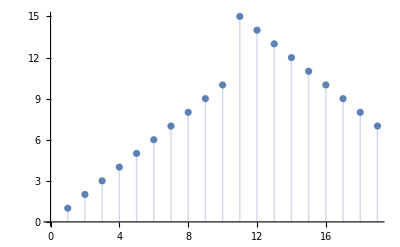

```mathematica
ListPlot[joined, Filling->Axis]
```

```mathematica
?Gather
```

Gather[list] gathers the elements of list into sublists of identical elements.
Gather[list,test] applies test to pairs of elements to determine if they should be considered identical.

```mathematica
Gather[joined ]
```

{{1},{2},{3},{4},{5},{6},{7,7},{8,8},{9,9},{10,10},{15},{14},{13},{12},{11}}

```mathematica
?Tally
```

Tally[list] tallies the elements in list, listing all distinct elements together with their multiplicities.
Tally[list,test] uses test to determine whether pairs of elements should be considered equivalent, and gives a list of the first representatives of each equivalence class, together with their multiplicities.

```mathematica
tally = Tally[joined]
```

{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,2},{8,2},{9,2},{10,2},{15,1},{14,1},{13,1},{12,1},{11,1}}

### Other useful operations

```mathematica
?RotateLeft
```

RotateLeft[expr,n] cycles the elements in expr n positions to the left. 
RotateLeft[expr] cycles one position to the left. 
RotateLeft[expr,{n_1,n_2,…}] cycles elements at successive levels n_i positions to the left.

```mathematica
range1
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
RotateLeft[range1]
```

{2,3,4,5,6,7,8,9,10,1}

```mathematica
?PadRight
```

PadRight[list,n] makes a list of length n by padding list with zeros on the right. 
PadRight[list,n,x] pads by repeating the element x. 
PadRight[list,n,{x_1,x_2,…}] pads by cyclically repeating the elements x_i. 
PadRight[list,n,padding,m] leaves a margin of m elements of padding on the left. 
PadRight[list,{n_1,n_2,…}] makes a nested list with length n_i at level i. 
PadRight[list] pads a ragged array list with zeros to make it full.

```mathematica
?PadLeft
```

PadLeft[list,n] makes a list of length n by padding list with zeros on the left. 
PadLeft[list,n,x] pads by repeating the element x. 
PadLeft[list,n,{x_1,x_2,…}] pads by cyclically repeating the elements x_i. 
PadLeft[list,n,padding,m] leaves a margin of m elements of padding on the right. 
PadLeft[list,{n_1,n_2,…}] makes a nested list with length n_i at level i. 
PadLeft[list] pads a ragged array list with zeros to make it full.

```mathematica
?Position
```

Position[expr,pattern] gives a list of the positions at which objects matching pattern appear in expr. 
Position[expr,pattern,levelspec] finds only objects that appear on levels specified by levelspec. 
Position[expr,pattern,levelspec,n] gives the positions of the first n objects found. 
Position[pattern] represents an operator form of Position that can be applied to an expression.

```mathematica
?RandomInteger
```

RandomInteger[{i_min,i_max}] gives a pseudorandom integer in the range {i_min,i_max}. 
RandomInteger[i_max] gives a pseudorandom integer in the range {0,…,i_max}. 
RandomInteger[] pseudorandomly gives 0 or 1. 
RandomInteger[range,n] gives a list of n pseudorandom integers. 
RandomInteger[range,{n_1,n_2,…}] gives an n_1×n_2×… array of pseudorandom integers.

```mathematica
RandomInteger[100, 20]
```

{2,86,30,41,69,18,34,42,18,41,24,95,39,30,74,57,90,10,40,1}

```mathematica
?Sort
```

Sort[list] sorts the elements of list into canonical order. 
Sort[list,p] sorts using the ordering function p.

```mathematica
Sort[RandomInteger[100, 20]]
```

{4,13,14,15,16,22,43,46,48,51,61,71,73,73,77,86,91,96,98,100}

```mathematica
?Reverse
```

Reverse[expr] reverses the order of the elements in expr. 
Reverse[expr,n] reverses elements at level n in expr.
Reverse[expr,{n_1,n_2,…}] reverses elements at levels n_1, n_2, … in expr.

```mathematica
Reverse[Sort[RandomInteger[100, 20]]]
```

{99,97,94,88,81,77,71,70,64,56,50,43,41,39,27,19,18,18,6,5}

```mathematica
?RandomSample
```

RandomSample[{e_1,e_2,…},n] gives a pseudorandom sample of n of the e_i.
RandomSample[{w_1,w_2,…}→{e_1,e_2,…},n] gives a pseudorandom sample of n of the e_i chosen using weights w_i.
RandomSample[{e_1,e_2,…}] gives a pseudorandom permutation of the e_i.

```mathematica
?SortBy
```

SortBy[list,f] sorts the elements of list in the order defined by applying f to each of them. 
SortBy[f] represents an operator form of SortBy that can be applied to an expression.

```mathematica
evens = Table[2 n, {n, 10}]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
odds = Table[2 n - 1, {n, 10}]
```

{1,3,5,7,9,11,13,15,17,19}

```mathematica
?Prime
```

Prime[n] gives the n^th prime number.

```mathematica
?Union
```

Union[list_1,list_2,…] gives a sorted list of all the distinct elements that appear in any of the list_i. 
Union[list] gives a sorted version of a list, in which all duplicated elements have been dropped.

```mathematica
Tuples[{a, b,c}, 3]
```

{{a,a,a},{a,a,0},{a,a,c},{a,0,a},{a,0,0},{a,0,c},{a,c,a},{a,c,0},{a,c,c},{0,a,a},{0,a,0},{0,a,c},{0,0,a},{0,0,0},{0,0,c},{0,c,a},{0,c,0},{0,c,c},{c,a,a},{c,a,0},{c,a,c},{c,0,a},{c,0,0},{c,0,c},{c,c,a},{c,c,0},{c,c,c}}

```mathematica
?Permutations
```

Permutations[list] generates a list of all possible permutations of the elements in list. 
Permutations[list,n] gives all permutations containing at most n elements.
Permutations[list,{n}] gives all permutations containing exactly n elements.

```mathematica
Permutations[{a, b, c}, {2}]
```

{{a,0},{a,c},{0,a},{0,c},{c,a},{c,0}}

```mathematica
Permutations[{a, b, c}, 2]
```

{{},{a},{0},{c},{a,0},{a,c},{0,a},{0,c},{c,a},{c,0}}

```mathematica
?Subsets
```

Subsets[list] gives a list of all possible subsets of list. 
Subsets[list,n] gives all subsets containing at most n elements. 
Subsets[list,{n}] gives all subsets containing exactly n elements. 
Subsets[list,{n_min,n_max}] gives all subsets containing between n_min and n_max elements. 
Subsets[list,nspec,s] limits the result to the first s subsets. 
Subsets[list,nspec,{s}] gives if possible the s^th subset.